```mathematica
g=(q*(x-x1)+r*(x-x1)^3)*Exp[-p*(x-x1)^2];
gi=(ⅇ^(-p (x1-xt)^2) (r+p (q+r (x1-xt)^2)))/(2 p^2);

Simplify[g/.x->x1]
Simplify[D[g, x]/.x->x1]
Simplify[∫_x1^(+∞) gⅆx]
Simplify[∫_xt^(+∞) gⅆx]
Simplify[∫_x1^(+∞) giⅆxt]
```

0

q

If[Re[p]>0,(p q+r)/(2 p^2),Integrate[ⅇ^(-p (x-x1)^2) (q+r (x-x1)^2) (x-x1),{x,x1,∞},Assumptions→Re[p]≤0]]

If[Re[p]>0,(ⅇ^(-p (x1-xt)^2) (r+p (q+r (x1-xt)^2)))/(2 p^2),Integrate[ⅇ^(-p (x-x1)^2) (q+r (x-x1)^2) (x-x1),{x,xt,∞},Assumptions→Re[p]≤0]]

If[Re[p]>0,(√π (2 p q+3 r))/(4 √p),Integrate[ⅇ^(-p (x1-xt)^2) (r+p (q+r (x1-xt)^2)),{xt,x1,∞},Assumptions→Re[p]≤0]]/(2 p^2)

```mathematica
Solve[{
q==(B0*2*π)/λu,
(p q+r)/(2 p^2)==(λu*B0)/(2*π),
((√π (2 p q+3 r))/(4 √p))/(2 p^2)==0
},{q,r,p}]
```

{{r→-(8 B0 π^3)/(9 λu^3),q→(2 B0 π)/λu,p→(2 π^2)/(3 λu^2)}}

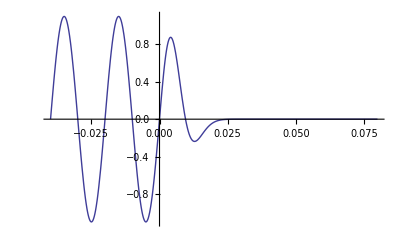

```mathematica
B0=1.1;
λu=0.02;
x1=0;
p=(2 π^2)/(3 λu^2);
q=(2 B0 π)/λu;
r=-(8 B0 π^3)/(9 λu^3);

FF[x_]:=If[x<x1,B0*Sin[(2*π)/λu*x],(q*(x-x1)+r*(x-x1)^3)*Exp[-p*(x-x1)^2]];

Plot[FF[x],{x,-2*λu,4*λu},PlotRange->All]
```

```mathematica
g=(q*(x-x1)+r*(x-x1)^3)*Exp[-p*(x-x1)^2];
gi=(ⅇ^(-p (x1-xt)^2) (-r-p (q+r (x1-xt)^2)))/(2 p^2);

Simplify[g/.x->x1]
Simplify[D[g, x]/.x->x1]
Simplify[∫_(-∞)^x1 gⅆx]
Simplify[∫_(-∞)^xt gⅆx]
Simplify[∫_(-∞)^x1 giⅆxt]
```

0

q

If[Re[p]>0,-(p q+r)/(2 p^2),Integrate[ⅇ^(-p (x-x1)^2) (q+r (x-x1)^2) (x-x1),{x,-∞,x1},Assumptions→Re[p]≤0]]

If[Re[p]>0,(ⅇ^(-p (x1-xt)^2) (-r-p (q+r (x1-xt)^2)))/(2 p^2),Integrate[ⅇ^(-p (x-x1)^2) (q+r (x-x1)^2) (x-x1),{x,-∞,xt},Assumptions→Re[p]≤0]]

If[Re[p]>0,-(√π (2 p q+3 r))/(4 √p),Integrate[ⅇ^(-p (x1-xt)^2) (-r-p (q+r (x1-xt)^2)),{xt,-∞,x1},Assumptions→Re[p]≤0]]/(2 p^2)

```mathematica
Solve[{
q==(B0*2*π)/λu,
-(p q+r)/(2 p^2)==(-λu*B0)/(2*π),
(-(√π (2 p q+3 r))/(4 √p))/(2*p^2)==0
},{q,r,p}]
```

{{r→-(8 B0 π^3)/(9 λu^3),q→(2 B0 π)/λu,p→(2 π^2)/(3 λu^2)}}

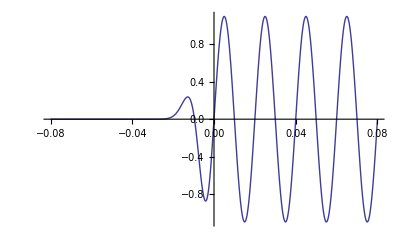

NIntegrate::inumr: The integrand 1.8478768058431807`*^-9 ⅇ^-16449.340668482262` xt^2 (3.7896560387033103`*^6 - 16449.340668482262` (345.57519189487726`  - 3.7896560387033103`*^6 xt^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.08`, -0.079`}}.

NIntegrate::inumr: The integrand 1.8478768058431807`*^-9 ⅇ^-16449.340668482262` xt^2 (3.7896560387033103`*^6 - 16449.340668482262` (345.57519189487726`  - 3.7896560387033103`*^6 xt^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.08`, -0.078`}}.

NIntegrate::inumr: The integrand 1.8478768058431807`*^-9 ⅇ^-16449.340668482262` xt^2 (3.7896560387033103`*^6 - 16449.340668482262` (345.57519189487726`  - 3.7896560387033103`*^6 xt^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.08`, -0.077`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

-Graphics-

```mathematica
B0=1.1;
λu=0.02;
x1=0;

p=(2 π^2)/(3 λu^2); (*(√(144-8 π^2))/λu;*)
q=(2 B0 π)/λu;(*(2 B0 (-18+π^2))/(π λu);*)
r=-(8 B0 π^3)/(9 λu^3);

(*
a=((676.8426868771007) B0)/λu^3;(*(16 B0 (-9+π^2))/(π λu^3);*)
b=(0.5 B0 ((701.9754281058191)-((4061.0561212626044) x1)/λu))/λu^2;(*(12 B0 (-4 (-9+π^2) x1+(-6+π^2) λu))/(π λu^3);*)
c=(B0 (6.283185307179586+((2030.5280606313022) x1^2)/λu^2-((701.9754281058191) x1)/λu))/λu; (*(2 B0 (24 (-9+π^2) x1^2-12 (-6+π^2) x1 λu+π^2 λu^2))/(π λu^3);*)
d=(0.5 B0 x1 (-12.566370614359172-((1353.6853737542015) x1^2)/λu^2+((701.9754281058191) x1)/λu))/λu;
*)
FFR[x_]:=If[x<x1,(q*(x-x1)+r*(x-x1)^3)*Exp[-p*(x-x1)^2],B0*Sin[(2*π)/λu*x]];
I1FF[x_]:=NIntegrate[FFR[xx],{xx,-4*λu,x}];
I2FF[x_]:=NIntegrate[gi,{xx,-4*λu,x}];

Plot[FFR[x],{x,-4*λu,4*λu},PlotRange->All]


ListPlot[Table[{x,I2FF[x]},{x,-4*λu,4*λu,λu/20.}],PlotRange->All,Joined->True]
```

```mathematica
CForm[q*(x-x1+λu/2)*Exp[p*(x-x1+λu/2)]]
```

(2*B0*Power(E,(Sqrt(144 - 8*Power(Pi,2))*(x - x1 + λu/2.))/λu)*(-18 + Power(Pi,2))*(x - x1 + λu/2.))/(Pi*λu)

```mathematica
N[Pi]
```

3.14159

```mathematica
3.141592653589793
```

```mathematica
N[-((17280-960 π^2)/(54-π^2))^(1/3)]
```

-5.61326